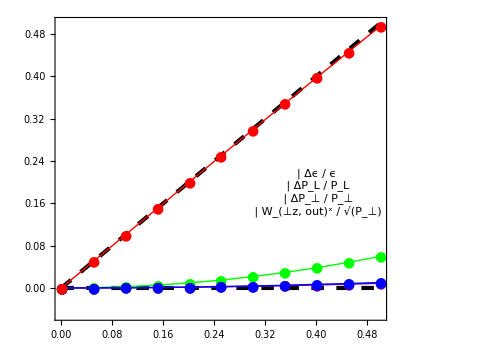

```mathematica
(*ANISOTROPIC HADRON RESONANCE GAS*)

T0 = 0.155;
αT = 1.118756;
αL = 0.7520408;
Λ = 0.1562006; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,-8.832*10^-5,0.0003533,0.0007949,0.001413,0.002208,0.00318,0.004329,0.005655,0.007158,0.008839};

ΔPLoverPLdata = {0.0,0.000595,0.00238,0.005356,0.009523,0.01488,0.02144,0.02919,0.03814,0.0483,0.05965};

ΔPToverPTdata ={0.0,0.0001028,0.0004112,0.0009253,0.001645,0.002571,0.003702,0.00504,0.006854,0.008335,0.01029};

Wxzdata = {0.0,0.04999,0.09996,0.1498,0.1996,0.2493,0.2988,0.3481,0.3971,0.4459,0.4944};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δϵ / ϵ",FontSize->16]},

{Graphics[{Green,Disk[]},ImageSize->10],Style["ΔP_L / P_L",FontSize->16]},{Graphics[{Blue,Disk[]},ImageSize->10],Style["ΔP_⊥ / P_⊥",FontSize->16]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["W_(⊥z, out)^x / √(P_⊥)",FontSize->16]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
Wxzplot = Table[{frac[[i]],Wxzdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.-0.05,0.5},ImageSize->{500,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔPLoverPLplot,Δϵoverϵplot,ΔPToverPTplot,Wxzplot},Joined->{True},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,14},{●,14},{●,14},{●,14}},PlotStyle->{{Green,Thick},{Purple,Thick},{Blue,Thick},{Red,Thick}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.4,0.18}]},ImageSize->{500,400},FrameLabel->{"W_(⊥z, in)^x / √(P_⊥)"}]
```